```mathematica
Clear[g]
```

```mathematica
Reduce[Fold[And,Table[Indexed[g,i]==(Indexed[a,i]*Indexed[b,i])/Indexed[c,i],{i,2}]]&&
g==Sum[Indexed[g,i],{i,1,2}],Table[Indexed[g,i],{i,1,2}]]
```

Reduce::itdim: The variable g has inconsistent dimensionality.

```mathematica
Eliminate[
Fold[And,Table[Indexed[g,i]>0,{i,2}]]&&
Fold[And,Table[Indexed[a,i]>0,{i,2}]]&&
Fold[And,Table[Indexed[b,i]>0,{i,2}]]&&
Fold[And,Table[Indexed[c,i]>0,{i,2}]]&&
Fold[And,Table[Indexed[g,i]==(Indexed[a,i]*Indexed[b,i])/Indexed[c,i],{i,2}]]&&
h==Sum[Indexed[g,i],{i,1,2}],h]
```

Eliminate::eqf: g>0 is not a well-formed equation.

Eliminate[g1>0&&g2>0&&a1>0&&a2>0&&b1>0&&b2>0&&c1>0&&c2>0&&g1==(a1 b1)/c1&&g2==(a2 b2)/c2&&h==g1+g2,h]

```mathematica
Table[Indexed[g,i]==(Indexed[a,i]*Indexed[b,i])/Indexed[c,i],{i,5}]
```

{g1==(a1 b1)/c1,g2==(a2 b2)/c2,g3==(a3 b3)/c3,g4==(a4 b4)/c4,g5==(a5 b5)/c5}

```mathematica
Eliminate[

Fold[And,Table[Indexed[g,i]==(Indexed[a,i]*Indexed[b,i])/Indexed[c,i],{i,2}]]&&
h==Sum[Indexed[g,i],{i,1,2}],Table[Indexed[c,i],{i,2}]]
```

g1+g2==h

```mathematica
allGraphs5GeneratorAtomKeys=Bases["G","AtomKeys"]
```

{29524,9841,22963,27337,28795,29281,29443,29497,29515,29521,29523,3037,7573,9085,9832,9838,9840,20767,22231,22882,22936,22962,26607,27094,27310,27334,28552,28714,28786,29191,29251,29280,29415,29440,29488,29511,760,2278,3036,6816,7570,9076,9828,20034,20740,22150,22854,26364,27064,28462,29160,0}

```mathematica
Bases["G","AtomKeys"]==allGraphs5GeneratorAtomKeys
```

False

```mathematica
FormulaGraphReverse[formula_]:=Block[{sets=Map[SymbolToSets[#]&,ListofVars[formula]], edges={},vertices,vert={}},
Table[
Table[
If[IsRefinement[s1,s2]&&(Length[s1]==Length[s2]-1), AppendTo[edges,SetsToSymbol[s1]->SetsToSymbol[s2]]]
,{s2,Select[sets,#≠s1&]}
]
,{s1,sets}];
vert = Table[SetsToSymbol[s],{s,sets}];
vertices = Table[SetsToSymbol[s]-> Rotate[SymbolToLabel[ SetsToSymbol[s]],Pi/6],{s,sets}];
Graph[vert,edges,VertexLabels->vertices, GraphLayout->"LayeredDigraphEmbedding"]
]
```

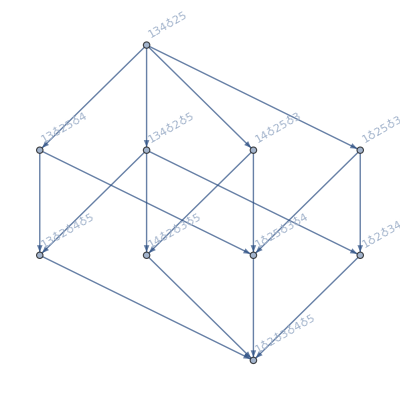
-Graphics-g134x25

```mathematica
Labeled[FormulaGraphReverse[allGraphs5[allGraphs5GeneratorAtomKeys[[45]],"colofour"]],allGraphs5[allGraphs5GeneratorAtomKeys[[45]],"colofourgenerator"]]
```

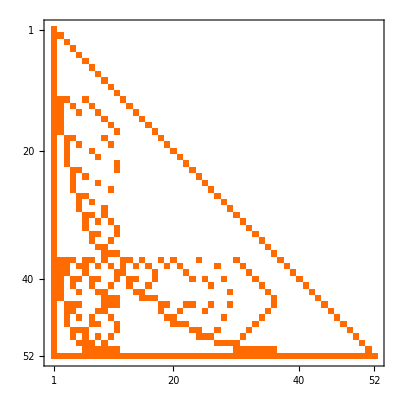

```mathematica
MatrixPlot[Table[BaseCoeff[k,"C"],{k,allGraphs5GeneratorAtomKeys}]]
```

```mathematica
ConversionMatrix["G","C"]//MatrixPlot
```

-Graphics-